```mathematica
SetDirectory[NotebookDirectory[]];
<<RLBotIO`
<<RLBotMisc`
```

```mathematica
AirTorque = {-400.0, -130.0, 95.0};
AirDamping  = {-50.0, -30.0, -20.0};
ωMaxAerial= 5.5;
αMax = 9.0;
J =10.5;
Δt = 1/60.0;

scale = DiagonalMatrix[{1/ωMaxAerial,1/ωMaxAerial,1/ωMaxAerial,1/π,1/π,1/π}];
```

```mathematica
getRPY[ω0_, ωT_, J_, θ_, Δt_] := Module[{
Ω0 = Transpose[θ].ω0, 
ΩT= Transpose[θ].ωT,
T = AirTorque,
H = AirDamping,
a,b,c
},
a = Table[Δt/J T[[i]], {i, 1, 3}];
b = Table[ -Δt/J H[[i]] Ω0[[i]], {i, 1, 3}];b[[1]] = 0;
c = Table[ΩT[[i]]-(1 + Δt/J H[[i]])Ω0[[i]], {i, 1, 3}];
Table[solvePWL[a[[i]], b[[i]], c[[i]]], {i, 1, 3}]
]

q[x_]:= 1-1/(1+500 x^2)
r[Δx_, v_]:=Δx-Sign[v] 1/2 v^2/αMax
controller[Δx_, v_, Δt_] := Module[{ri,a, rf},
ri=r[Δx, v];
a = Sign[ri]αMax ;
rf = r[Δx-v Δt,v+a Δt];
If[ri * rf < 0,a(2 ri/(ri-rf)-1),a]
]

OrientationController[s_] := Module[{ω, θ,α,Δθ, ϕLocal, ϕWorld, error},
ω = s[[1;;3]];
θ = AxisAngleRotation[s[[4;;6]]];
Δθ=Transpose[θ];
ϕLocal=RotationAxis[Δθ];
ϕWorld=θ.ϕLocal;

error = Abs[ϕWorld] + Abs[ω];

α =  Table[q[error[[i]]]controller[ϕWorld[[i]],ω[[i]], Δt],{i,1,3}];
getRPY[ω, ω + α Δt, J, θ, Δt] 
]
```

SetDelayed::write: Tag Real in (-0.0548611)[Δx_,v_] is Protected.

$Failed

```mathematica
Clear[y]
```

```mathematica
T = DiagonalMatrix[{T1, T2, T3}];
H = DiagonalMatrix[{D1, D2, D3} * {1,(1-Abs[p]), (1-Abs[y])}];
```

```mathematica
AirDamping
```

{-50.,-30.,-20.}

```mathematica
Clear[r]
```

```mathematica
T.{r, p, y} + H.{ωr, ωp, ωy}
```

{r T1+D1 ωr,p T2+D2 ωp (1-Abs[p]),T3 y+D3 ωy (1-Abs[y])}

```mathematica
Solve[r T1+D1 ωr == A1, r]
```

{{r→(A1-D1 ωr)/T1}}

```mathematica
Accelerations[{u1_, u2_, u3_}] := Module[{T, H},
T = DiagonalMatrix[{T1, T2, T3}];
H = DiagonalMatrix[{D1, D2, D3} * {1,(1-Abs[u2]), (1-Abs[u3])}];
T.{u1, u2, u3}+H.{ω1, ω2, ω3}
]

torques = Thread[{T1, T2, T3, D1, D2, D3} -> Join[AirTorque, AirDamping]];
{
Chop[Accelerations[{#, 0, 0}][[1]]]& /@ {-1, 0, 1},
Chop[Accelerations[{0, #, 0}][[2]]]& /@ {-1, 0, 1},
Chop[Accelerations[{0, 0, #}][[3]]]& /@ {-1, 0, 1}
}

{{-T1+D1 ω1,D1 ω1,T1+D1 ω1},{-T2,D2 ω2,T2},{-T3,D3 ω3,T3}} /. torques
```

{{-T1+D1 ω1,D1 ω1,T1+D1 ω1},{-T2,D2 ω2,T2},{-T3,D3 ω3,T3}}

{{400.-50. ω1,-50. ω1,-400.-50. ω1},{130.,-30. ω2,-130.},{-95.,-20. ω3,95.}}

```mathematica
nextState[s_, a_] := Module[
{T, H, τ, ω, θ},
ω = s[[1;;3]];
θ = AxisAngleRotation[s[[4;;6]]];
T = DiagonalMatrix[AirTorque];
H = DiagonalMatrix[AirDamping * {1,(1-Abs[a[[2]]]), (1-Abs[a[[3]]])}];
τ = θ.(T.a+H.Transpose[θ].ω);
ω = ω + τ/J Δt ;
ω *= Min[1.0, ωMaxAerial/Norm[ω]];
θ = RotationAxis[AxisAngleRotation[(ω-τ/(2J)Δt)  Δt].θ];
Join[ω, RotationAxis[θ]]
]
```

```mathematica
OrientationController2[s_] := Module[{ω,ωpara,θ,α,Δθ,ϕLocal,ϕWorld, error},
ω = Z[s[[4;;6]]].s[[1;;3]];
ϕWorld=-s[[4;;6]];
ωpara=ω.Normalize[ϕWorld];
getRPY[s[[1;;3]], s[[1;;3]]+9Normalize[ϕWorld]Δt, J, AxisAngleRotation[s[[4;;6]]], Δt]
]
```

```mathematica
states[[4,1;;3]]/states[[5,4;;6]]
```

{-0.0866799,-0.0861532,-0.0835661}

```mathematica
n = Normalize[RandomReal[{-1, 1}, 3]]
```

{0.623023,0.673055,0.398547}

```mathematica
Clear[a2]
```

```mathematica
A = Ω[{a1, a2, a3}]
```

{{0,-a3,a2},{a3,0,-a1},{-a2,a1,0}}

```mathematica
B = Ω[{b1, b2, b3}]
```

{{0,-b3,b2},{b3,0,-b1},{-b2,b1,0}}

```mathematica
AntisymmetricAxis[A.B-B.A]
```

{-a3 b2+a2 b3,a3 b1-a1 b3,-a2 b1+a1 b2}

```mathematica
Cross[{a1, a2, a3}, {b1, b2, b3}]
```

{-a3 b2+a2 b3,a3 b1-a1 b3,-a2 b1+a1 b2}

```mathematica
LinearSolve[B[3n]
```

```mathematica
RandomBangBangTrajectory[s0_: {0, 0, 0, 0, 0, 0}] := Module[{s, a,r, states, actions, rewards, count},
s = If[s0 == {0, 0, 0, 0, 0, 0}, RandomState[], s0];
a = OrientationController[s];
r = 0.0;

states = {s};
actions = {a};
rewards = {{r}};

Do[
a = OrientationController[s];
s = nextState[s, a];
r -= Δt;
AppendTo[states,s];
AppendTo[actions,a];
AppendTo[rewards,{r}];
If[Norm[s[[1;;3]]]<0.01 && Norm[s[[4;;6]]]<0.01 , Break[]]
,
{240}
];

{states, actions, Reverse[rewards]}
]
```

```mathematica
Join[{}, {5}]
```

{5}

```mathematica
batchedStates = {};
batchedActions = {};
batchedRewards = {};
```

```mathematica
Do[
{states, actions, rewards} = RandomBangBangTrajectory[];
batchedStates= Join[batchedStates, states];
batchedActions= Join[batchedActions, actions];
batchedRewards= Join[batchedRewards, rewards];
,
{2}
]
Length[batchedStates]
```

127

```mathematica
batchedStates[[1]]
```

{3.66543,1.78893,0.2356,-1.29642,-2.44275,0.217037}

```mathematica
valueNetwork=NetChain[{256,Ramp,64,Ramp,64,Tanh, 1},"Input"->6M];
policyNetwork=NetChain[{256,Ramp,64,Ramp,64,Tanh,3},"Input"->6M];
```

```mathematica
valueNetwork =  NetTrain[
valueNetwork,
(SparseEncode[#,M] &/@(batchedStates.scale))->batchedRewards,
MaxTrainingRounds->256,
BatchSize->4096,
"TargetDevice"->"GPU"
];
```

```mathematica
policyNetwork =  NetTrain[
policyNetwork,
(SparseEncode[#,M] &/@(batchedStates.scale))->batchedActions,
MaxTrainingRounds->256,
BatchSize->4096,
"TargetDevice"->"GPU"
];
```

```mathematica
gridpoints = Flatten[Table[{0, 0, 0, x, y, 0}, {x, -2, 2, 0.1}, {y, -2, 2, 0.1}], 1];
arrows = evaluate[policyNetwork, gridpoints];
```

```mathematica
arrows
```

{{-0.296885,-0.544593,-0.0725322},{-0.28374,-0.519423,-0.124629},{-0.269387,-0.481492,-0.161516},1675,{0.251459,0.597459,-0.10124},{0.18789,0.63209,-0.0974052},{0.129,0.667292,-0.0839081}}
 |  |  |  |

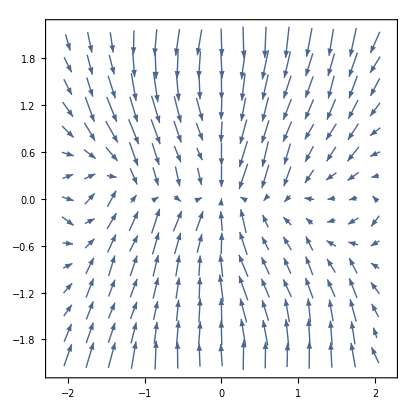

```mathematica
gridpoints = Flatten[Table[{0, 0, 0, x, y, 0}, {x, -2, 2, 0.1}, {y, -2, 2, 0.1}], 1];
arrows = evaluate[policyNetwork, gridpoints];
datapoints = Table[{gridpoints[[i, 4;;5]], -arrows[[i,1;;2]]}, {i, 1, Length[gridpoints]}];
ListVectorPlot[datapoints, PlotLegends->Automatic]
```

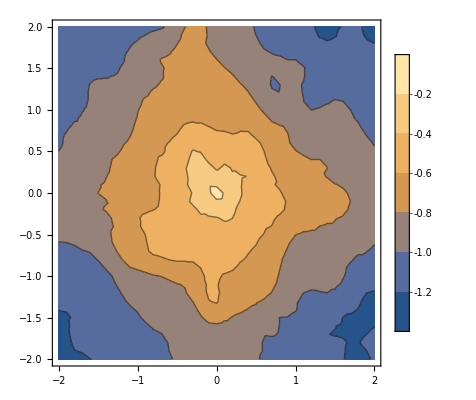

```mathematica
gridpoints = Flatten[Table[{0, 0, 0, x, y, 0}, {x, -2, 2, 0.1}, {y, -2, 2, 0.1}], 1];
values = evaluate[valueNetwork, gridpoints];
datapoints = Table[{gridpoints[[i, 4]], gridpoints[[i, 5]], values[[i,1]]}, {i, 1, Length[gridpoints]}];
ListContourPlot[datapoints, PlotLegends->Automatic]
```

```mathematica
evaluate[network_, arg_]:= If[TensorRank[arg] == 1,
network[SparseEncode[arg.scale,M]],
network@(SparseEncode[#,M]&/@(arg.scale))
]
```

```mathematica
trainNetwork[network_, inputs_, outputs_, n_] := NetTrain[
network,
(SparseEncode[#,M] &/@inputs)->outputs,
MaxTrainingRounds->n,
BatchSize->2048
]
```

{-0.0281647}

{{-1.,-1.,-0.777735},{-1.,-0.9,-0.66183},{-1.,-0.8,-0.573623},{-1.,-0.7,-0.534231},{-1.,-0.6,-0.516963},431,{1.,0.6,-0.620945},{1.,0.7,-0.684237},{1.,0.8,-0.707966},{1.,0.9,-0.819721},{1.,1.,-0.846756}}
 |  |  |  |

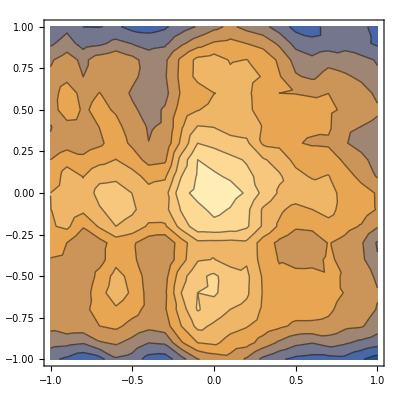

```mathematica
valueNetwork[SparseEncode[{0, 0, 0, 0, 0, 0}, M] ]
```

```mathematica
RandomState[] := Module[{s = RandomReal[{-1, 1}, 6] * {ωMaxAerial, ωMaxAerial, ωMaxAerial, π, π, π}},
While[Norm[s[[1;;3]]] > ωMaxAerial || Norm[s[[4;;6]]] ≥ π,
s = RandomReal[{-1, 1}, 6] * {ωMaxAerial, ωMaxAerial, ωMaxAerial, π, π, π}
];
s
]
```

```mathematica
Z[θ_] := Module[{Ω0=Ω[θ]},IdentityMatrix[3] - Ω0/2 + (Ω0.Ω0)/12-(Ω0.Ω0.Ω0.Ω0)/720]
```

```mathematica
Comm[X_,Y_]:=Y.X-X.Y
f[{θ0_,θ1_,θ2_,ω0_,ω1_,ω2_}, {u0_, u1_, u2_}]:=Module[{(*Ω0, Ω1, Θ, T, H*)},
Ω0=Ω[{θ0,θ1,θ2}]; 
Ω1=Ω[{ω0,ω1,ω2}];
Θ = AxisAngleRotation[{θ0,θ1,θ2}];
T = DiagonalMatrix[AirTorque];
H = DiagonalMatrix[AirDamping *{1, 0, 0}];
Join[
AntisymmetricAxis[Ω1+1/2 Comm[Ω0,Ω1]+1/12 Comm[Ω0,Comm[Ω0,Ω1]]-1/720 Comm[Ω0,Comm[Ω0,Comm[Ω0,Comm[Ω0,Ω1]]]]],
1/J Θ.(T.{u0, u1, u2}+H.Transpose[Θ].{ω0,ω1,ω2})
]
]
```

```mathematica
fx[{θ0_,θ1_,θ2_,ω0_,ω1_,ω2_}, {u0_, u1_, u2_}] :=Module[{
f0 = f[{θ0,θ1,θ2,ω0,ω1,ω2}, {u0, u1, u2}], 
II = IdentityMatrix[6],
ϵ=0.001
},
Transpose[Table[
(f[{θ0,θ1,θ2,ω0,ω1,ω2}+ϵ II[[i]], {u0, u1, u2}]-f0)/ϵ,
{i, 1, 6}
]]
]

uOptimal[{θ0_,θ1_,θ2_,ω0_,ω1_,ω2_}, {p0_,p1_,p2_,p3_,p4_,p5_}] :=Module[{Θ, T, q},
Θ = AxisAngleRotation[{θ0,θ1,θ2}];
T = DiagonalMatrix[AirTorque];
q = {p3,p4,p5}.Θ.T;
q/Max[Max[Abs[q]],0.000001]
(*Sign[{p3,p4,p5}.Θ.T]*)
]
```

```mathematica
Ω1=Ω[ω Δt];
Ω0=Ω[ϕ0];
ϕ1-ϕ0
ω Δt
AntisymmetricAxis[Ω1+1/2 Comm[Ω0,Ω1]]
AntisymmetricAxis[Ω1+1/2 Comm[Ω0,Ω1]+1/12 Comm[Ω0,Comm[Ω0,Ω1]]]
AntisymmetricAxis[Ω1+1/2 Comm[Ω0,Ω1]+1/12 Comm[Ω0,Comm[Ω0,Ω1]]-1/720 Comm[Ω0,Comm[Ω0,Comm[Ω0,Comm[Ω0,Ω1]]]]]
```

{0.00263405,0.0258686,0.00481254}

{0.0033248,0.0125163,0.002327}

{0.00179227,0.012755,0.00323249}

{0.0013915,0.0129092,0.00251353}

{0.00133922,0.0129294,0.00241975}

```mathematica
Ω0 =Ω[{θ0,θ1,θ2}];
Ω1 =Ω[{ω0,ω1,ω2}];
tmp = FullSimplify[D[AntisymmetricAxis[Ω1+1/2 Comm[Ω0,Ω1]+1/12 Comm[Ω0,Comm[Ω0,Ω1]]-1/720 Comm[Ω0,Comm[Ω0,Comm[Ω0,Comm[Ω0,Ω1]]]]], {{ω0,ω1,ω2}}]]
```

{{1/720 (720-θ1^4-θ2^2 (60+θ0^2+θ2^2)-θ1^2 (60+θ0^2+2 θ2^2)),θ2/2+1/720 θ0 θ1 (60+θ0^2+θ1^2+θ2^2),1/720 (-360 θ1+θ0 (60+θ0^2+θ1^2) θ2+θ0 θ2^3)},{-θ2/2+1/720 θ0 θ1 (60+θ0^2+θ1^2+θ2^2),1/720 (720-θ0^4-θ2^2 (60+θ1^2+θ2^2)-θ0^2 (60+θ1^2+2 θ2^2)),1/720 (360 θ0+θ1 (60+θ0^2+θ1^2) θ2+θ1 θ2^3)},{1/720 (360 θ1+θ0 (60+θ0^2+θ1^2) θ2+θ0 θ2^3),1/720 (-360 θ0+θ1 (60+θ0^2+θ1^2) θ2+θ1 θ2^3),1/720 (720-θ0^4-θ1^2 (60+θ1^2+θ2^2)-θ0^2 (60+2 θ1^2+θ2^2))}}

```mathematica
Controller[s_] := Module[{ω, θ,α,Δθ, ϕLocal, ϕWorld, error},
ω = s[[1;;3]];
θ = AxisAngleRotation[s[[4;;6]]];
Δθ=Transpose[θ];
ϕLocal=RotationAxis[Δθ];
ϕWorld=θ.ϕLocal;

error = Abs[ϕWorld] + Abs[ω];

α =  Table[q[error[[i]]]controller[ϕWorld[[i]],ω[[i]], Δt],{i,1,3}];
getRPY[ω, ω + α Δt, J, θ, Δt] 
]
```

```mathematica
Simulate[s0_: {0, 0, 0, 0, 0, 0}] := Module[{s,a,t,states,actions,rewards,count},
s = If[s0 == {0, 0, 0, 0, 0, 0}, RandomState[], s0];
a = OrientationController[s];
t = 0.0;

states = {s};
actions = {a};

Do[
a = Controller[s];
s = nextState[s, a];
t+= Δt;
AppendTo[states,s];
AppendTo[actions,a];
If[Norm[s[[1;;3]]]<0.01 && Norm[s[[4;;6]]]<0.01 , Break[]]
,
{240}
];

{states, actions, t}
]
```

```mathematica
G[ω_] := 1/2((Sign[ω] ω^2)/9.0)
Gprime[ω_] := (ω Sign[ω])/9.0+0.03
```

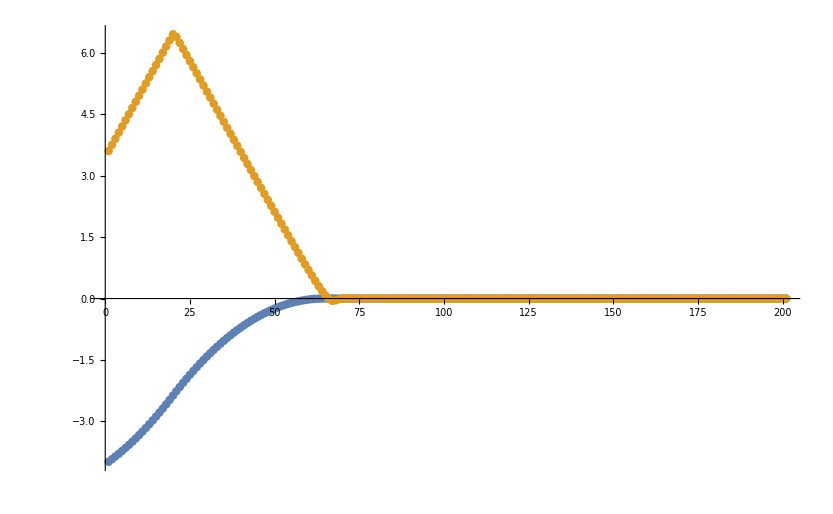

```mathematica
ϕ=2.3-2π;
ω=3.6;

history = {{ϕ, ω}};
Do[
α = Clip[1/(Gprime[ω] dt)(-ϕ - ω dt - G[ω]), {-9.0, 9.0}];
ω += α dt;
ϕ += ω dt;
AppendTo[history, {ϕ, ω}],
{i, 1, 200}
];

ListPlot[Transpose[history], PlotRange->All]

(*Graphics[{
Point[{0, 0}],
Line[history]
}, PlotRange->{{-3,3}, {-5, 5}}]*)
```

```mathematica
torques
```

{T1→-400.,T2→-130.,T3→95.,D1→-50.,D2→-30.,D3→-20.}

```mathematica
{{-T1+D1 ω1,D1 ω1,T1+D1 ω1},{-T2,D2 ω2,T2},{-T3,D3 ω3,T3}} /. torques
GetControlForAcceleration[α_, values_] := Module[{αclipped = Clip[α, {Min[values], Max[values]}]},
If[Min[values[[1;;2]]] ≤ αclipped ≤Max[values[[1;;2]]],
If[Abs[values[[2]]-values[[1]]] < 10^-4, -0.5, (αclipped- values[[2]])/(values[[2]]-values[[1]]) ],
If[Abs[values[[3]]-values[[2]]] < 10^-4, 0.5, (αclipped- values[[2]])/(values[[3]]-values[[2]]) ]
]
]
```

{{400.-50. ω1,-50. ω1,-400.-50. ω1},{130.,-30. ω2,-130.},{-95.,-20. ω3,95.}}

```mathematica
possibleα
```

{{38.0952,0.,-38.0952},{12.381,-2.85714 ω2,-12.381},{-9.04762,-1.90476 ω3,9.04762}}

```mathematica
GetControlForAcceleration[(-ϕ - ω dt - Sign[ω]GRoll[ω])/((Sign[ω]GRoll'[ω]+0.03) dt), possibleα[[1]]]
```

{55.3273,38.0952}

-1.

```mathematica
ϕ=-2.3;
ω=2.0;
possibleα =1/J{{-T1+D1 ω,D1 ω,T1+D1 ω},{-T2,D2 ω2,T2},{-T3,D3 ω3,T3}} /. torques;
u = GetControlForAcceleration[(-ϕ - ω dt - GRoll[ω])/(DGRoll[ω] dt), possibleα[[1]]];
```

-1.

-1.

-1.

«80 more identical outputs»

-0.774192

-0.559691

-0.344205

-0.233925

-0.173877

-0.138689

-0.116014

-0.0996624

-0.0864762

-0.0748306

-0.0638843

-0.0531987

-0.0425435

-0.0317961

-0.0208898

-0.00978654

0.0943166

0.461536

0.611264

0.692295

0.742893

0.777343

0.802188

0.820847

0.835279

0.846685

0.855843

0.863277

0.869352

0.87433

0.8784

0.881703

0.884346

0.886405

0.88794

0.888993

0.889592

0.889754

0.889487

0.888789

0.887647

0.886039

0.883931

0.881276

0.878013

0.874061

0.869312

0.863631

0.856838

0.848696

0.838895

0.827011

0.812471

0.794474

0.771892

0.74311

0.705793

0.656587

0.590885

0.503254

0.390419

0.260166

0.142034

0.0698125

0.0389495

0.0243776

0.0155692

0.0100145

0.0064696

0.0041901

0.00271806

0.00176492

0.00114675

0.000745396

0.000484641

0.000315158

0.000204967

0.000133312

0.0000867116

0.0000564024

0.0000366882

0.0000238649

0.0000155238

0.0000100981

6.5687×10^-6

4.2729×10^-6

2.77949×10^-6

1.80805×10^-6

1.17612×10^-6

7.65064×10^-7

4.9767×10^-7

3.23732×10^-7

2.10587×10^-7

1.36986×10^-7

8.91086×10^-8

5.79647×10^-8

3.77059×10^-8

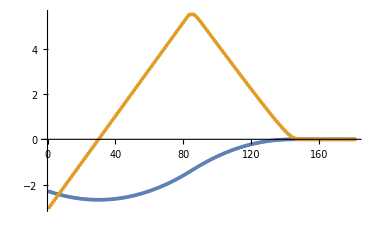

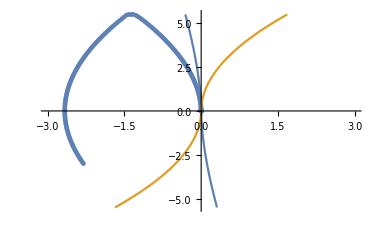

```mathematica
ϕ=-2.3;
ω=-3.0;

history = {{ϕ, ω}};
Do[
possibleα =1/J{{-T1+D1 ω,D1 ω,T1+D1 ω},{-T2,D2 ω,T2},{-T3,D3 ω,T3}} /. torques;
(*u = GetControlForAcceleration[(-ϕ - ω dt - GRoll[ω])/(DGRoll[ω] dt), possibleα[[1]]];
{ω,ϕ} =nextState[{ω,0,0,ϕ,0,0}, {u,0, 0}][[{1,4}]];*)

u = GetControlForAcceleration[(-ϕ - ω dt - GPitch[ω])/(DGPitch[ω] dt), possibleα[[2]]];
{ω,ϕ} =nextState[{0,ω,0,0,ϕ,0}, {0,u, 0}][[{2,5}]];
Print[u];
(*u = GetControlForAcceleration[(-ϕ - ω dt - GYaw[ω])/(DGYaw[ω] dt), possibleα[[3]]];
{ω,ϕ} =nextState[{0, 0,ω,0,0,ϕ}, {0,0, u}][[{3,6}]];*)
AppendTo[history, {ϕ, ω}],
{i,1,180}
];

ListPlot[Transpose[history], PlotRange->All]
Show[
ListPlot[history, PlotRange->All],
ParametricPlot[{
{-GRoll[ω],ω}/. {b->50/10.5, T->400/10.5},
{1/2((Sign[ω] ω^2)/9.0), ω}
}, {ω, -5.5, 5.5}
],
 PlotRange->{{-3, 3}, {-5.5, 5.5}}
]
```

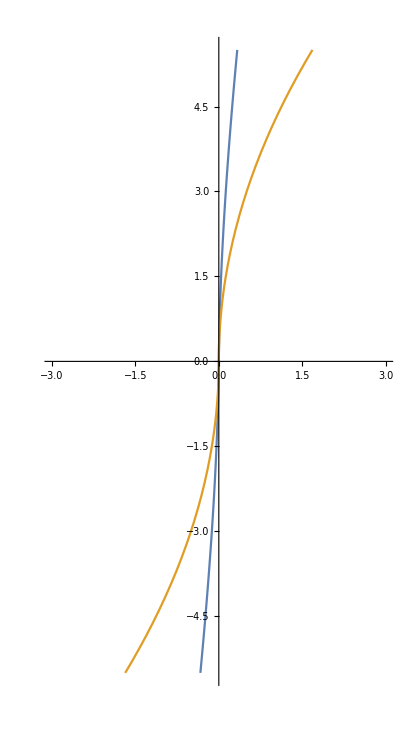

```mathematica
Show[
ParametricPlot[{
{GRoll[ω],ω},
{1/2((Sign[ω] ω^2)/9.0), ω}
}, {ω,-5.5,5.5}
],
 PlotRange->{{-3, 3}, {-5.5, 5.5}}
]
```

```mathematica
AirTorque = {-400.0, -130.0, 95.0};
AirDamping  = {-50.0, -30.0, -20.0};
```

```mathematica
y1[τ_] = DSolve[{z''[τ]==T,z'[0]==0, z[0] == 0}, z, τ] [[1,1,2,2]];
y2[τ_] = DSolve[{z''[τ]+b z'[τ]==T,z'[0]==0, z[0] == 0}, z, τ] [[1,1,2,2]];
```

```mathematica
Clear[T]
```

```mathematica
dt
```

0.0166667

```mathematica
rollParameters = {T ->400.0/10.5, b -> 50.0/10.5};
GRoll[ω_] :=(RealSign[ω] (b RealAbs[ω]+T Log[T/(T+b RealAbs[ω])])/b^2 + 0.006 ω)/. rollParameters
DGRoll[ω_] := (FullSimplify[D[GRoll[zz], zz], Assumptions->zz≠ 0] /. zz->ω )/. rollParameters;


pitchParameters = {T ->130.0/10.5};
GPitch[ω_] :=( 1/2((RealSign[ω] ω^2)/T)+ 0.01 ω)/.pitchParameters
DGPitch[ω_] := (FullSimplify[D[GPitch[zz], zz], Assumptions->zz≠ 0] /. zz->ω )/.pitchParameters;

yawParameters = {T ->95.0/10.5};
GYaw[ω_] :=( 1/2((RealSign[ω] ω^2)/T)+ 0.01 ω)/.yawParameters
DGYaw[ω_] := (FullSimplify[D[GYaw[zz], zz], Assumptions->zz≠ 0] /. zz->ω )/.yawParameters;
```

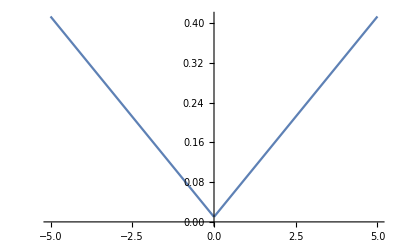

```mathematica
Plot[DGPitch[ω], {ω, -5, 5}]
```

```mathematica
{ω,ϕ}={-5.5, 0};
history1 = {{ϕ, ω}};
Do[
{ω,ϕ} =nextState[{ω,0,0,ϕ,0,0}, {-1,0, 0}][[{1,4}]];
AppendTo[history1, {ϕ, ω}];
If[ω > 5.4999, Break[]]
,
{i, 1, 100}
]
{ω,ϕ}={5.5, 0};
history2 = {{ϕ, ω}};
Do[
{ω,ϕ} =nextState[{ω,0,0,ϕ,0,0}, {1,0, 0}][[{1,4}]];
AppendTo[history2, {ϕ, ω}];
If[ω < -5.4999, Break[]]
,
{i, 1, 100}
]
ϕOffset = -0.2694141371393828;
```

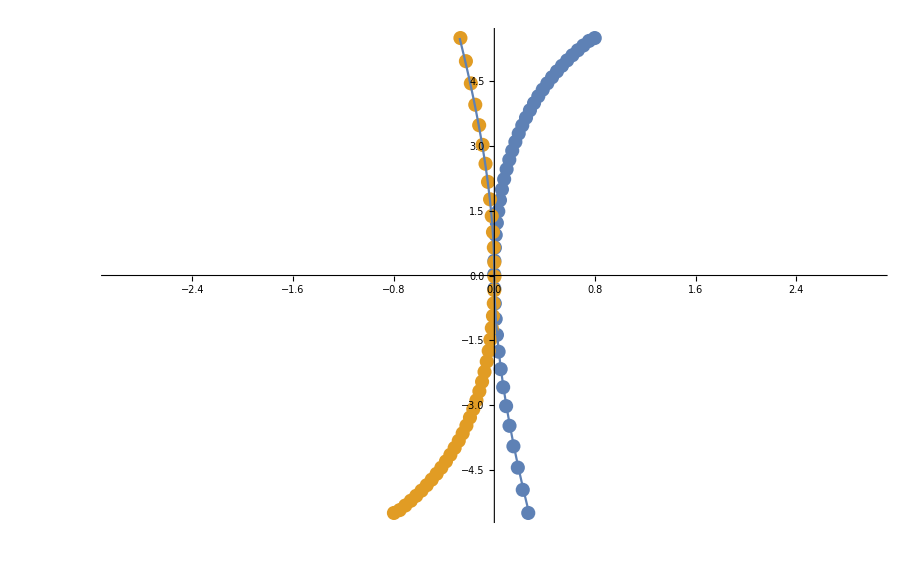

```mathematica
Show[
ListPlot[{
# - {ϕOffset, 0}& /@ history1,
# + {ϕOffset, 0}& /@ history2
}],
ParametricPlot[{
{GRoll[ω],ω}/. {b->50/10.5, T->400/10.5}
}, {ω, -5.5, 5.5}
],
 PlotRange->{{-3, 3}, {-5.5, 5.5}}
]
```